```mathematica
delta = 0.000001
```

1.×10^-6

```mathematica
maxx=10
```

10

```mathematica
s = NDSolve[{chi''[x] == chi[x]^(3/2)/Sqrt[x], chi[delta]== 1, chi'[delta] == -1.586}, chi,  {x, delta, maxx}]
```

{{chi→InterpolatingFunction[…]}}

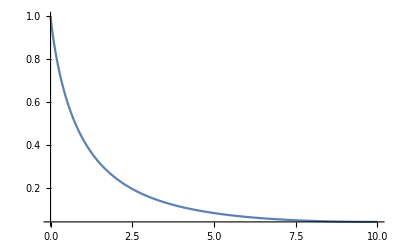

```mathematica
Plot[Evaluate[chi[x] /. s], {x, delta, maxx}, PlotRange -> All]
```

```mathematica
alpha = z ^(1/3) 2 (4/(3 Pi))^(2/3)
```

(4 2^(1/3) z^(1/3))/(3 π)^(2/3)

```mathematica
veff[x_] :=-z/x Evaluate[chi[alpha x] /. s]
```

```mathematica
z = 1
```

1

```mathematica
veff[2]
```

{-0.107688}

```mathematica
-1/3 chi[(4 6^(1/3))/π^(2/3)]
```

-1/3 chi[(4 6^(1/3))/π^(2/3)]

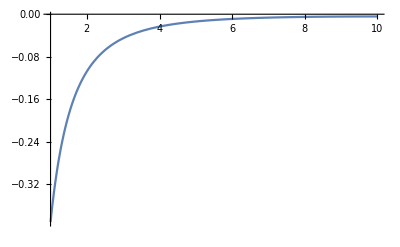

```mathematica
Plot[veff[x], {x, delta + 1, maxx}, PlotRange -> All]
```

```mathematica
vext[r_] := (- z)/r
```

```mathematica
vind[r_] := veff[r] - vext[r]
```

```mathematica
n[r_] := ((3/(5 ak))(- veff[r]))^(3/2)
```

```mathematica
ak = 3/10(3 Pi ^2)^(2/3)
```

3/10 3^(2/3) π^(4/3)

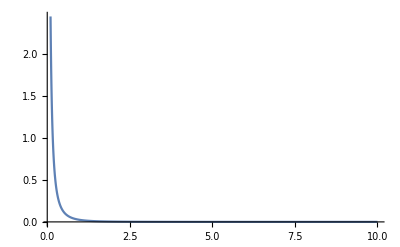

```mathematica
Plot[n[r], {r, 0.1, maxx}, PlotRange-> All]
```

```mathematica
NIntegrate[4 Pi r ^2  n[r], {r,delta ,10}]
```

{0.998389}

```mathematica
ttotal =ak NIntegrate[4Pi r^2 n[r] ^(5/3), {r, delta, maxx}]
```

{0.767752}